### Export helper function import.

```mathematica
<<peeters`

peeters`setGitDir["../project/figures/phy487-qmsolids"]

fs=Style[#,FontSize->14]&;
```

peeters`

/Users/pjoot/project/figures/phy487-qmsolids

### Global variables and functions (closed)

```mathematica
Clear[debyeTemperatures];

(* bulk-initialization-of-associative-array-hash-implemented-with-function-pattern *)
debyeTemperatures=Dispatch[{
(*IBach and Luth 4th ed.*)
"KCl"->235,"NaCl"->321,"LiCl"->422,"LiF"->732,

(* data from: http://www.knowledgedoor.com/2/elements_handbook/debye_temperature.html *)
"Aluminum"->433,"Americium"->121,"Antimony"->220,"Argon"->92.0,"Arsenic"->282,"Barium"->111,"Beryllium"->1481,"Bismuth"->120,"Boron"->1480,"Cadmium"->210,"Calcium"->229,"Carbon"->2230,"Carbon-diamond"->2230,"Carbon-graphite"->413,"Cerium"->179,"Cesium"->40.5,"Chromium"->606,"Cobalt"->460,"Copper"->347,"Curium"->123,"Dysprosium"->183,"Erbium"->188,"Europium"->118,"Francium"->39,"Gadolinium"->182,"Gallium"->325,"Germanium"->373,"Gold"->162.3,"Hafnium"->252,"Holmium"->190,"Hydrogen"->122,"Indium"->112,"Iodine"->109,"Iridium"->420,"Iron"->477,"Krypton"->71.9,"Lanthanum"->150,"Lead"->105,"Lithium"->344,"Lutetium"->183,"Magnesium"->403,"Manganese"->409,"Mercury"->72,"Molybdenum"->423,"Neodymium"->163,"Neon"->74.6,"Neptunium"->259,"Nickel"->477,"Niobium"->276,"Osmium"->467,"Palladium"->271,"Platinum"->237,"Plutonium"->206,"Potassium"->91.1,"Praseodymium"->152,"Protactinium"->185,"Radium"->89,"Rhenium"->416,"Rhodium"->512,"Rubidium"->56.5,"Ruthenium"->555,"Samarium"->169,"Scandium"->346,"Selenium"->152.5,"Silicon"->645,"Silver"->227.3,"Sodium"->156.5,"Strontium"->147,"Tantalum"->246,"Technetium"->454,"Tellurium"->152,"Terbium"->176,"Thallium"->78.5,"Thorium"->160,"Thulium"->200,"Tin"->199,"Titanium"->420,"Tungsten"->383,"Uranium"->248,"Vanadium"->399,"Xenon"->64.0,"Ytterbium"->118,"Yttrium"->248,"Zinc"->329,"Zirconium"->290,

"Actinium"->Missing["NotAvailable"],"Astatine"->Missing["NotAvailable"],"Berkelium"->Missing["NotAvailable"],"Bohrium"->Missing["NotAvailable"],"Bromine"->Missing["NotAvailable"],"Californium"->Missing["NotAvailable"],"Chlorine"->Missing["NotAvailable"],"Copernicium"->Missing["NotAvailable"],"Darmstadtium"->Missing["NotAvailable"],"Dubnium"->Missing["NotAvailable"],"Einsteinium"->Missing["NotAvailable"],"Fermium"->Missing["NotAvailable"],"Fluorine"->Missing["NotAvailable"],"Hassium"->Missing["NotAvailable"],"Helium"->Missing["NotAvailable"],"Lawrencium"->Missing["NotAvailable"],"Meitnerium"->Missing["NotAvailable"],"Mendelevium"->Missing["NotAvailable"],"Nitrogen"->Missing["NotAvailable"],"Nobelium"->Missing["NotAvailable"],"Oxygen"->Missing["NotAvailable"],"Phosphorus"->Missing["NotAvailable"],"Polonium"->Missing["NotAvailable"],"Promethium"->Missing["NotAvailable"],"Radon"->Missing["NotAvailable"],"Roentgenium"->Missing["NotAvailable"],"Rutherfordium"->Missing["NotAvailable"],"Seaborgium"->Missing["NotAvailable"],"Sulfur"->Missing["NotAvailable"],"Ununhexium"->Missing["NotAvailable"],"Ununoctium"->Missing["NotAvailable"],"Ununpentium"->Missing["NotAvailable"],"Ununquadium"->Missing["NotAvailable"],"Ununseptium"->Missing["NotAvailable"],"Ununtrium"->Missing["NotAvailable"]

(* ,_-> Missing["NotAvailable"]*)
} ];

Clear[ debyeElementKeys ] ;
debyeElementKeys = {"Aluminum","Americium","Antimony","Argon","Arsenic","Barium","Beryllium","Bismuth","Boron","Cadmium","Calcium","Carbon","Cerium","Cesium","Chromium","Cobalt","Copper","Curium","Dysprosium","Erbium","Europium","Francium","Gadolinium","Gallium","Germanium","Gold","Hafnium","Holmium","Hydrogen","Indium","Iodine","Iridium","Iron","Krypton","Lanthanum","Lead","Lithium","Lutetium","Magnesium","Manganese","Mercury","Molybdenum","Neodymium","Neon","Neptunium","Nickel","Niobium","Osmium","Palladium","Platinum","Plutonium","Potassium","Praseodymium","Protactinium","Radium","Rhenium","Rhodium","Rubidium","Ruthenium","Samarium","Scandium","Selenium","Silicon","Silver","Sodium","Strontium","Tantalum","Technetium","Tellurium","Terbium","Thallium","Thorium","Thulium","Tin","Titanium","Tungsten","Uranium","Vanadium","Xenon","Ytterbium","Yttrium","Zinc","Zirconium"} ;

Clear[debyeTemperature]
debyeTemperature[s_] := s/. debyeTemperatures ;

Clear[debyePlot]
debyePlot[e_] := Module[{points, symbols, g, interestingMins, interestingMaxes},
interestingMaxes = ElementData[#,"AtomicNumber"] &/@ {"C", "Si", "Cr", "Ru", "Os", "Np"} ;
interestingMins = ElementData[#,"AtomicNumber"] &/@ { "H", "Ne", "K", "Rb", "In", "Cs", "Eu", "Yb", "Hg", "Fr"} ;

symbols = Map[ {Style[ElementData[#, "Symbol"], 15], {#, debyeTemperature[ElementData[#, "StandardName"]]  }} &,e] ;
points = Flatten[{#[[2]]} &/@ symbols, 1] ;

(*symbols*)
g= ListLinePlot[ points
, AxesLabel->{"Z", "Debye temp (K)"}
(*, Frame->True*)
,Epilog->{
(*PointSize[Large],*) (* good for Mathematica display, but not when saved for use in latex *)
(*Point[# ]&/@points,*) 
orbi[#] &/@ points,
(* Style 15 modification of text also good for Mathematica display, but not for generated .eps *)
Text[ ElementData[#, "Symbol"](*Style[, 15]*), {#, 75 + debyeTemperature[ElementData[#, "StandardName"]]}] &/@ interestingMaxes,
Text[ ElementData[#, "Symbol"](*Style[, 15]*),  {#, -75 +debyeTemperature[ElementData[#, "StandardName"]]}] &/@ interestingMins
},
PlotRange -> {Full, {-100, 2500}}] ;

g

] ;

Clear[orbitalColors] ;
orbitalColors = { 
{#-> Darker[Yellow] (*s*)}&/@{1, 2, 3, 4, 11, 12, 19, 20, 37, 38, 55, 56, 87, 88 } , 
{#-> Darker[Green] (*p*)}&/@ Flatten[{Range[5, 10], Range[ 13, 18], Range[ 31, 36], Range[ 49, 54], Range[81, 86]}] ,
{#-> Darker[Blue](*d*)}&/@ Flatten[{Range[21, 30], Range[39, 48], 57, Range[72, 80], 89, Range[104, 106]}] ,
{#-> Darker[Orange] (*f*)}&/@ Flatten[{Range[58, 71], Range[90, 103]}] 
} // Flatten ;

Clear[orbi]
orbi[s_(*, scale_ : 1*)] := {s[[1]] /. orbitalColors, Point[s](*Point[s[[1]], s[[2]]/scale]*)} ;
(*Attributes[orb]={Listable};*)
(*orbi[{3, 5}]*)

Clear[radialPlot]
radialPlot[e_] := Module[{points, symbols, g, interestingMins, interestingMaxes},
interestingMins = ElementData[#,"AtomicNumber"] &/@ {"H","C", "Si", "Cr", "Ru", "Os", "Ne", "Cl", "Br", "I"} ;
interestingMaxes = ElementData[#,"AtomicNumber"] &/@ {  "K", "Rb", "In", "Cs", "Eu", "Yb", "Hg", "Li", "Na"} ;

symbols = Map[ {Style[ElementData[#, "Symbol"], 15], {#, ElementData[#, "AtomicRadius"]  }} &,e] ;
points = Flatten[{#[[2]]} &/@ symbols, 1] ;

(*symbols*)
g= ListLinePlot[ points
, AxesLabel->{"Z", "Atomic Radius"}
(*, Frame->True*)
,Epilog->{
(*PointSize[Large],*) (* good for Mathematica display, but not when saved for use in latex *)
(*Point[# ]&/@points,*) 
orbi[#] &/@ points
,
(* Style 15 modification of text also good for Mathematica display, but not for generated .eps *)
Text[ ElementData[#, "Symbol"](*Style[, 15]*), {#, 15 + ElementData[#, "AtomicRadius"]}] &/@ interestingMaxes,
Text[ ElementData[#, "Symbol"](*Style[, 15]*),  {#, -15 +ElementData[#, "AtomicRadius"]}] &/@ interestingMins
}
, PlotRange -> {Full, {0, 320}}
] ;
g

] ;

Clear[ radialElementKeys ] ;radialElementKeys = {"Aluminum","Antimony","Argon","Arsenic","Barium","Beryllium","Bismuth","Boron","Cadmium","Calcium","Carbon","Cesium","Chromium","Cobalt","Copper","Dysprosium","Erbium","Europium","Gadolinium","Gallium","Germanium","Gold","Hafnium","Holmium","Hydrogen","Indium","Iodine","Iridium","Iron","Krypton","Lead","Lithium","Lutetium","Magnesium","Manganese","Mercury","Molybdenum","Neodymium","Neon","Nickel","Niobium","Osmium","Palladium","Platinum","Potassium","Praseodymium","Rhenium","Rhodium","Rubidium","Ruthenium","Samarium","Scandium","Selenium","Silicon","Silver","Sodium","Strontium","Tantalum","Technetium","Tellurium","Terbium","Thallium","Thulium","Tin","Titanium","Tungsten","Vanadium","Xenon","Ytterbium","Yttrium","Zinc","Zirconium" } ;

Clear[mergePlots, maxR, maxD]
maxR = ElementData[ "Cesium", "AtomicRadius" ] ;
maxD = "Carbon"  /. debyeTemperatures ;
mergePlots[r_] := Module[{info, i,j,tips, scaleD},
scaleD = 5. ;
info = 
{#, ElementData[ #, "Symbol" ], ElementData[ #, "AtomicRadius" ], ElementData[#, "StandardName"] /. debyeTemperatures } & /@ r ;
iRadius =  DeleteCases[ info, {_, _, Missing[_], _}] ;
iDebye =  DeleteCases[ info, {_, _, _, Missing[_]}] ;

tRadius = Tooltip[ {#[[1]], maxR /#[[3]]}, Row[{#[[2]],", r = ",#[[3]], " pm"}] ] & /@ iRadius  ;
pRadius = {#[[1]] /. orbitalColors, Point[  {#[[1]], maxR/#[[3]]} ]}&  /@ iRadius ;

tDebye = Tooltip[ {#[[1]], scaleD(#[[4]]/maxD)}, Row[{#[[2]],", dT = ",#[[4]], " K"}] ] & /@ iDebye  ;
pDebye = {#[[1]] /. orbitalColors, Point[  {#[[1]], scaleD(#[[4]]/maxD)} ]}&  /@ iDebye ;

ListLinePlot[
{tRadius, tDebye}
,PlotMarkers->{Automatic,1/10}
,AxesLabel->{"Z"(*, "Atomic Radius"*)}
,Epilog->{ (*PointSize[Small],*)pRadius, pDebye  }
, Ticks ->{Automatic, None},
PlotRange -> Full
] 
]
```

### First two plots

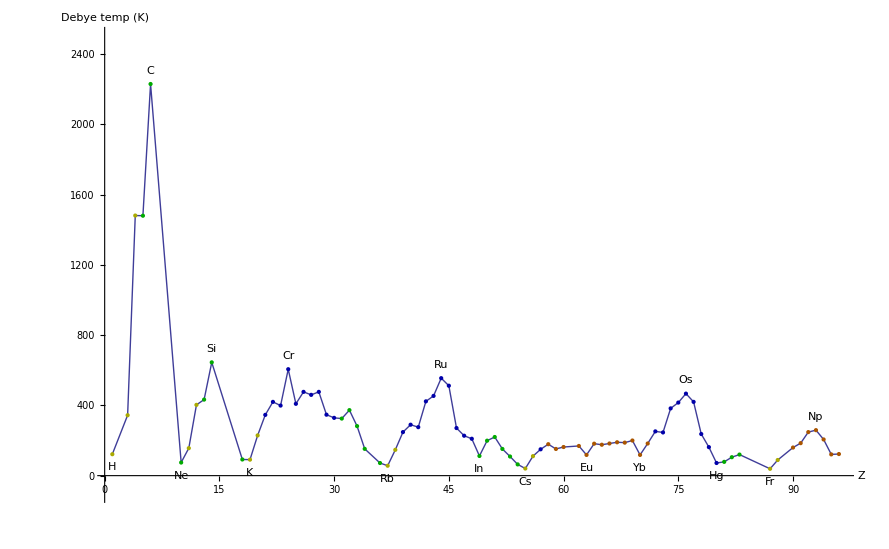

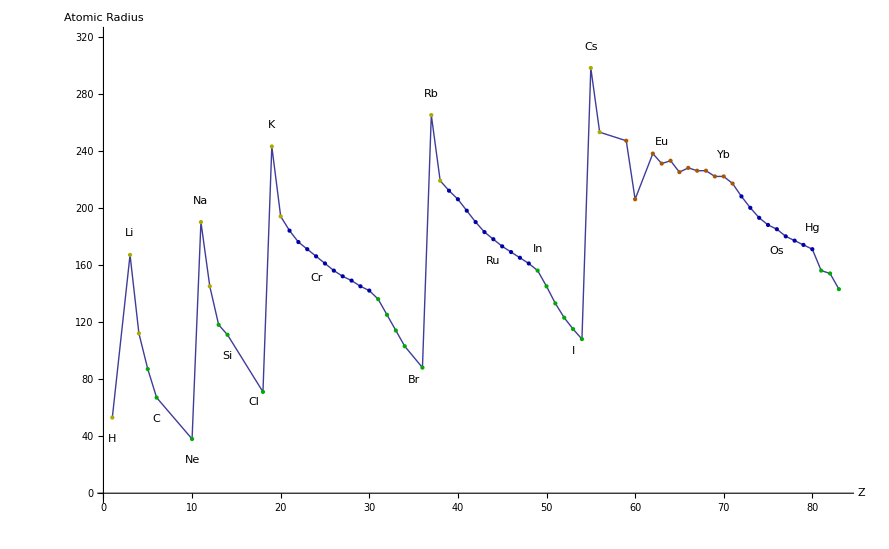

```mathematica
Clear[p] ;
p = debyePlot[ Sort[ ElementData[ #, "AtomicNumber" ] &/@ debyeElementKeys ]]  ;
p

Clear[p2] ;
p2 = radialPlot[ Sort[ ElementData[ #, "AtomicNumber" ] &/@ radialElementKeys ]]  ;
p2
```

### Merge plots (getting fancy)

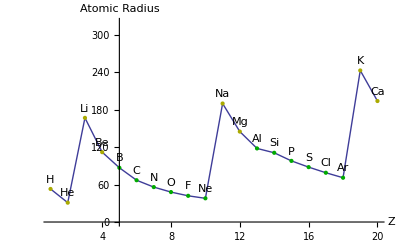

```mathematica
Clear[r]
r = DeleteCases[ 
{#, ElementData[ #, "Symbol" ], ElementData[ #, "AtomicRadius" ]} & /@ Range[20]
, {_, _, Missing[_]} ] ;

(* /. Missing[_] -> -1 ;*)
(*Cases[r,{ a_, b_,d_, c_}/;c > 0 ] [[All, {1,2,3, 4}]] *)

Clear[t]
t = Tooltip[ {#[[1]], #[[3]]}, #[[2]] ] & /@ r ;

(* An atomic radius plotting function that isn't selective for labelling *)
Clear[ radialPlot2 ]
(* i = {{Z, Symbol, Radii}, ...} *)
(*radialPlot2[i_] := *)
Module[{i, e, points, t, p, tips},
i = DeleteCases[ 
{#, ElementData[ #, "Symbol" ], ElementData[ #, "AtomicRadius" ]} & /@ Range[20]
, {_, _, Missing[_]} ] ;
e = i[[All, 1]] ;
points = i[[All,{1,3}]] ;
t = Text[ #[[2]], {#[[1]], 15 + #[[3]]}] & /@ i ;
(*tips = Tooltip[ {#[[1]], #[[3]]}, #[[2]] ] & /@ i ;*)
p = orbi[#] &/@ points ;

ListLinePlot[ points 
, AxesLabel->{"Z", "Atomic Radius"}
(*, Frame->True*)
,Epilog->{ p , t }
,PlotRange -> {Full, {0, 320}}
] 
] 
(*radialPlot2[ r ]*)
```

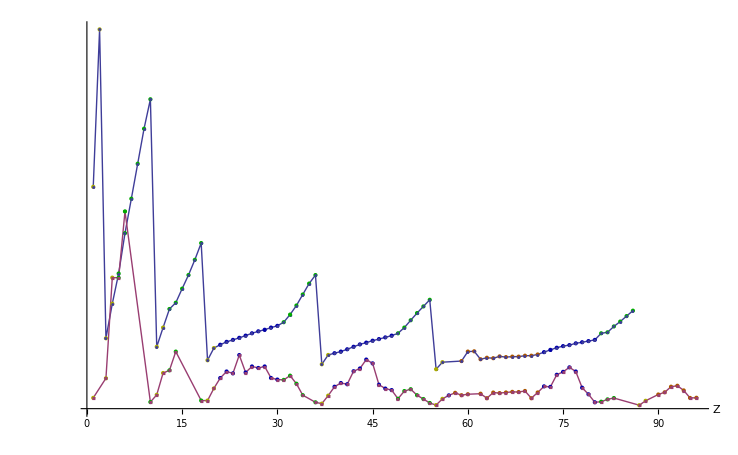

```mathematica
Clear[p3]
p3 = mergePlots[Range[103]]
```

### Export rules

```mathematica
(*peeters`exportForLatex["DebyeTemperaturesVsAtomicNumberFig1", p]*)
(*peeters`exportForLatex["atomicRadiiVsAtomicNumberFig2", p2]*)
(*peeters`exportForLatex["atomicInvRadiusAndDebyeTempOverlappedFig4", p3]*)
(*peeters`exportForLatex["ZlessThan20Radii", s]*)
```

### Scratch stuff.

```mathematica
(*ElementData[]
ElementData[ "Properties"]
ChemicalData[ "Properties"]*)
(*ElementData[ "Carbon", "AtomicRadius", "Units" ]*)

(*ListLinePlot[
Table[Tooltip[{j, j^2}, j^2], {j, 10}]
,PlotMarkers->{Automatic,1} (* tooltip seems to require this, even with Points in the epilog *)
,Epilog->{
PointSize[Large],
Table[
{RGBColor[RandomReal[], RandomReal[], RandomReal[]],
Point[{j, j^2}]},
{j, 10}
]  
}
] *)

(*ElementData[ "Carbon", "Name" ]
ElementData[ "Carbon", "StandardName" ]
ElementData[ All,"StandardName" ]
ElementData[ "Carbon", "Abbreviation" ]

"Aluminum"/.debyeTemperatures
"NaCl"/.debyeTemperatures
*)
(*ElementData[3, "StandardName" ]*)

(*ElementData[#,"StandardName"] &/@ Range[96] /. debyeTemperatures*)

(*Clear[debyeByAtomicNumber] ;
debyeByAtomicNumber = {ElementData[#, "AtomicNumber"], debyeTemperature[#]}  &/@ debyeElementKeys
*)
(*ElementData[ #, "AtomicNumber" ] &/@ debyeElementKeys*)

(*{ElementData[ #, "AtomicRadius" ], #} &/@ radialElementKeys*)
```